# 3D Cellular Automaton

Adrienne Lai

Mentor: Sylvia Haas

## Project Description

I first became interested in cellular automata when I learned about Conway’s Game of Life, and I was interested in Wolfram Language’s machine learning and graphics, so I was very excited for this project. The 3D Cellular Automata project uses machine learning to classify the general shape of 3D models generated by cellular automata and specifically looks for rules that generate irregular shapes. In order to achieve my goals, I trained a function to recognize familiar shapes like spheres and cubes from 3D models that have the general shape of the 3D figures. Additionally, I generated both a training and testing set of cellular automata models to run through the machine learning. Also, a function that uses the rules of specific cellular automata has been constructed to generate the locations of each cell.

## Cellular Automata

A cellular automaton is a set of rules iteratively applied to a configuration of cells. This means that the automaton changes during each iteration as the states of the cells change based on the rules. For example, if one cell is alive at the beginning and the rule is to change a cell to become alive if its neighboring cells are alive, then in the next iteration the four cells next to the first cell will be alive.

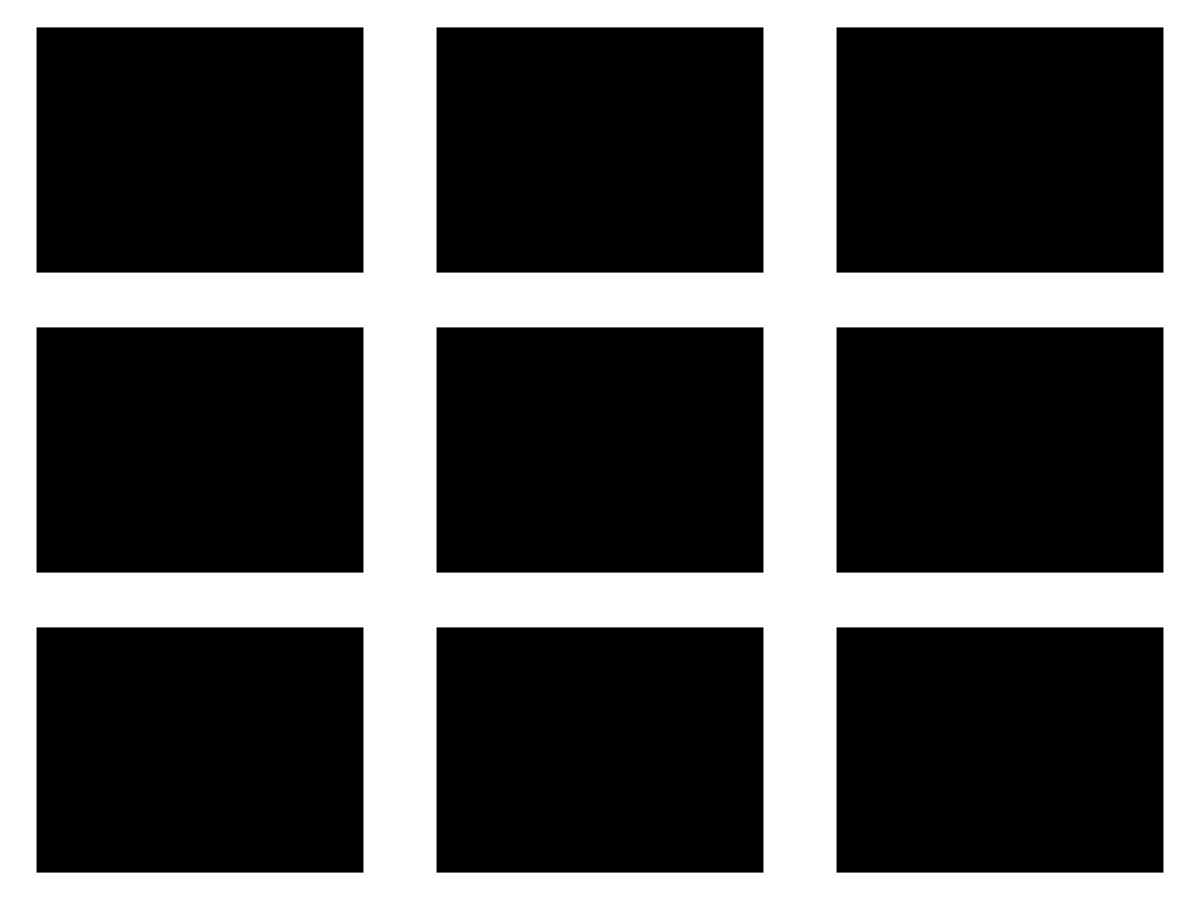
-Graphics--Graphics--Graphics-

### Different Types of Cellular Automata

I started the project by finding different ways to generate 3D cellular automata to use as my training and testing sets.

#### Rule #

I started by looking at Wolfram Documentation and found this code that generates models of cellular automata rule 126 of iterations from 0 to 11.

```mathematica
Image3D[#, ImageSize -> 150] & /@CellularAutomaton[{126, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},11]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Game of Life

Then, I found code that generates different iterations of the game of life with random starting configurations.

```mathematica
Manipulate[Image3D[
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{RandomInteger[1,{15,15}],0},n] ,
ImageSize-> {320,320}],
{n,0,500,1}, SaveDefinitions->True]
```

#### Code from A New Kind of Science

Next, I discovered this code that generates a cube from “A New Kind of Science” by Stephen Wolfram.

```mathematica
Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{1}|>,{{{{1}}},0},10]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

In the same book, there was a cellular automata that generates a sphere shape.

```mathematica
Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},9]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Finally, there was code for irregular shapes.

```mathematica
Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"OuterTotalisticCode"->16382|>,{{{{1}}},0},9]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},9]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Problem with k

After I collected code to produce figures from cellular automata rules, I started to go through the rules (n), states(k), and iterations(t) with a Manipulate to find combinations that generated different shapes for my training set.

```mathematica
Manipulate[Image3D[#, ImageSize -> 150] & /@CellularAutomaton[{x, {k, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}], {x,2,255, 1}, {k, 2, 255, 1}, {t, 0, 50, 1}]
```

However, I discovered that not all of the rules produce figures when k=2, or there are two possible states for a cell. Thus, I went through each rule and found which states applies to it and stored the data in an association.

```mathematica
ruleKVal = <|2->{2}, 6->{2}, 10-> {2}, 12 -> {3}, 14->{2}, 15->{3}, 18 -> {2}, 20 -> {4}, 21 -> {3}, 22 -> {2}, 26 ->{2}, 30 -> {2,3,5}, 36 -> {4}, 38 -> {2}, 39 -> {3}, 42 -> {2,3,6}, 46 -> {2, 46}, 48 -> {3, 6}, 50 -> {2}, 52 -> {4}, 54 -> {2}, 55 -> {5}, 56 -> {7}, 57 -> {3}, 58 -> {2}, 62 -> {2}, 66 -> {2, 3}, 68 -> {4}, 70 -> {2}, 72 -> {8}, 74 -> {2}, 75 -> {3}, 78 -> {2, 3, 6}, 80 -> {5, 8}, 82 -> {2}, 84 -> {3, 4, 6}, 86 -> {2}, 87 -> {2}, 90 -> {2, 9}, 93 -> {3}, 94 -> {2}, 96 -> {3}, 98 -> {2}, 100 -> {4}, 102 -> {2, 3}, 105 -> {3, 5, 7}, 106 -> {2}, 110 -> {2, 10}, 111 -> {3}, 114 -> {2, 3, 6}, 116 -> {4}, 118 -> {2}, 120 -> {3, 4, 10}, 122 -> {2}, 123 -> {3}, 126 -> {2}, 129 -> {3}, 132 -> {3, 4, 11}, 134 -> {2}, 136 -> {8}, 138 -> {2, 3}, 140 -> {5}, 142 -> {2}, 147 -> {3}, 148 -> {4}, 150 -> {2, 3, 6}, 154 -> {2, 7}, 155 -> {5}, 156 -> {3, 4, 12}, 158 -> {2}, 159 -> {3}, 164 -> {4}, 165 -> {3, 5}, 166 -> {2}, 168 -> {3, 4, 12}, 170 -> {2}, 171 -> {9}, 174 -> {2, 3}, 177 -> {3}, 178 -> {2}, 180 -> {4, 5, 9}, 182 -> {2, 13}, 183 -> {3}, 186 -> {2, 3, 6}, 190 -> {2, 5}, 192 -> {2}, 194 -> {2}, 195 -> {3, 13}, 196 -> {4}, 198 -> {2}, 200 -> {8}, 201 -> {3}, 202 -> {2}, 203 -> {7}, 204 -> {3, 4}, 205 -> {5}, 206 -> {2}, 210 -> {2, 3, 5}, 212 -> {4}, 213 -> {3}, 214 -> {2}, 218 -> {2}, 219 -> {3}, 222 -> {2, 3, 6}, 226 -> {2}, 228 -> {3, 4}, 230 -> {2, 6}, 231 -> {3}, 234 -> {2, 6}, 237 -> {3}, 238 -> {2}, 240 -> {3, 5}, 242 -> {2}, 244 -> {4}, 246 -> {2, 4}, 248 -> {4}, 250 -> {2}, 252 -> {4, 7, 9}, 254 -> {2}, 255 -> {3, 5}|>;
```

I found that rules 2 - 254 going up by 4 operate with the principle that each cell can be in two possible states. Additionally, if n = k, then the rule produces the same figures as n = 2 and k = 2. Therefore, they are not included in the association.

I met with Nikki and she said that when the k value changes, the type of cellular automata changes as well, so I should keep it consistent. So, I needed an association by k values as the keys.

Previous association with decimal place keys for the rules with more than one k value

```mathematica
ruleKVal2 = <|2->{2}, 6->{2}, 10-> {2}, 12 -> {3}, 14->{2}, 15->{3}, 18 -> {2}, 20 -> {4}, 21 -> {3}, 22 -> {2}, 26 ->{2}, 30 -> {2}, 30.1->{3}, 30.2 ->{5}, 36 -> {4}, 38 -> {2}, 39 -> {3}, 42 -> {2}, 42.1 ->{3},42.2 ->{6}, 46 -> {2}, 48 -> {3}, 48.1 ->{6}, 50 -> {2}, 52 -> {4}, 54 -> {2}, 55 -> {5}, 56 -> {7}, 57 -> {3}, 58 -> {2}, 62 -> {2}, 66 -> {2}, 66.1 ->{3}, 68 -> {4}, 70 -> {2}, 72 -> {8}, 74 -> {2}, 75 -> {3}, 78 -> {2}, 78.1 -> {3}, 78.2 ->{ 6}, 80 -> {5}, 80.1 ->{8}, 82 -> {2}, 84 -> {3}, 84.1 ->{4}, 84.2 -> {6}, 86 -> {2}, 87 -> {3}, 90 -> {2}, 90.1 ->{9}, 93 -> {3}, 94 -> {2}, 96 -> {3}, 98 -> {2}, 100 -> {4}, 102 -> { 2}, 102.2 ->{ 3}, 105 -> {3}, 105.1 ->{5}, 105.2 -> {7}, 106 -> {2}, 110 -> {2}, 110 ->{ 10}, 111 -> {3}, 114 -> {2}, 114.1 ->{3}, 114.2 -> {6}, 116 -> {4}, 118 -> {2}, 120 -> {3}, 120.1 -> {4},120.2 ->{ 10}, 122 -> {2}, 123 -> {3}, 126 -> {2}, 129 -> {3}, 132 -> {3},132.1 -> {4}, 132.2 ->{ 11}, 134 -> {2}, 136 -> {8}, 138 -> {2}, 138.1 ->{ 3}, 140 -> {5}, 142 -> {2}, 147 -> {3}, 148 -> {4}, 150 -> {2},150.1 ->{ 3},150.2->{ 6}, 154 -> {2},154.1->{ 7}, 155 -> {5}, 156 -> {3}, 156.1 ->{4}, 156.1 ->{12}, 158 -> {2}, 159 -> {3}, 164 -> {4}, 165 -> {3},165.1->{ 5}, 166 -> {2}, 168 -> {3}, 168.1 ->{4},168.2 -> {12}, 170 -> {2}, 171 -> {9}, 174 -> {2},174.1->{ 3}, 177 -> {3}, 178 -> {2}, 180 -> {4}, 180.1 ->{ 5}, 180.2 ->{9}, 182 -> {2},182.1->{ 13}, 183 -> {3}, 186 -> {2}, 186.1 ->{3},186.2->{ 6}, 190 -> {2},190.1->{ 5}, 192 -> {3}, 194 -> {2}, 195 -> {3},195.1->{ 13}, 196 -> {4}, 198 -> {2}, 200 -> {8}, 201 -> {3}, 202 -> {2}, 203 -> {7}, 204 -> {3},204.1->{ 4}, 205 -> {5}, 206 -> {2}, 210 -> {2},210.1->{ 3},210.1->{ 5}, 212 -> {4}, 213 -> {3}, 214 -> {2}, 218 -> {2}, 219 -> {3}, 222 -> {2},22.2->{ 3},22.3-> {6}, 226 -> {2}, 228 -> {3},228.1->{ 4}, 230 -> {2},230.1->{ 5}, 231 -> {3}, 234 -> {2},234.1->{ 6}, 237 -> {3}, 238 -> {2}, 240 -> {3},240.1->{ 5}, 242 -> {2}, 244 -> {4}, 246 -> {2},246.1->{ 3}, 248 -> {4}, 250 -> {2}, 252 -> {4},252->{ 7},252.2->{ 9}, 254 -> {2}, 255 -> {3, 5}|>;
```

List of rules that have possible states other than k = n.

```mathematica
rules = Keys[ruleKVal]
```

{2,6,10,12,14,15,18,20,21,22,26,30,36,38,39,42,46,48,50,52,54,55,56,57,58,62,66,68,70,72,74,75,78,80,82,84,86,87,90,93,94,96,98,100,102,105,106,110,111,114,116,118,120,122,123,126,129,132,134,136,138,140,142,147,148,150,154,155,156,158,159,164,165,166,168,170,171,174,177,178,180,182,183,186,190,192,194,195,196,198,200,201,202,203,204,205,206,210,212,213,214,218,219,222,226,228,230,231,234,237,238,240,242,244,246,248,250,252,254,255}

Function to get the rules of with a particular k value.

```mathematica
rules2[k_]:= Select[ruleKVal2, SameQ[#,{k}]&]//Keys //Floor
```

## Machine Learning

I decided to focus on shapes of cellular automata with two possible states 2, so I collected all of the rule numbers with k =2.

```mathematica
k2rules =<| 2 -> rules2[2]|>
```

<|2→{2,6,10,14,18,22,26,30,38,42,46,50,54,58,62,66,70,74,78,82,86,90,94,98,102,106,114,118,122,126,134,138,142,150,154,158,166,170,174,178,182,186,190,194,198,202,206,210,214,218,222,226,230,234,238,242,246,250,254}|>

Next, I made the training set of cellular automata figures using a Manipulate to generate cellular automaton models when k = 2 and rule selections are only from rules with k = 2. (All when only 1 initial cell alive).

```mathematica
Manipulate[Image3D[#, ImageSize -> 250] & /@CellularAutomaton[{x, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}], {x, k2rules[[Key[2]]]}, {t, 2, 35, 1}]
```

### Training Sets

Function to generate the figures of different cellular automata with rule n, k colors, and t iteration.

```mathematica
caVal[{n_, k_, t_}] := Image3D[#, ImageSize -> 100] & /@CellularAutomaton[{n, {k, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}];
```

#### Cube training

List of cellular automata parameters (n, k, t) with a cube shape.

```mathematica
cV = {{2, 2, 15}, {2, 2, 30}, {6, 2, 7},{6, 2, 27},  {2, 2, 29},{14,2,4}, {18, 2, 6}, {14, 2, 14}, {22, 2, 10}, {22, 2, 23}, {70, 2, 4}, {18,2,3}, {6, 2, 27},{82,2,2}, {6, 2, 3}, {170, 2, 5}, {10, 2, 7}, {150, 2, 2}};
```

List of the figures generated by the cV cellular automaton parameters.

```mathematica
cT = caVal[#] & /@ cV
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

#### Sphere training

List of cellular automata parameters (n, k, t) with a sphere shape.

```mathematica
sV = {{6, 2, 8},{22, 2, 8}, {22, 2, 9},{20, 4, 12}, {54, 2, 8}, {54, 2, 9}, {70, 2, 8}, {150, 2, 8}, {150, 2, 16}, {150,2,9}};
```

List of images generated by sV cellular automaton parameters and cellular automaton shapes from “A New Kind of Science” that look like spheres.

```mathematica
sT = Join[caVal[#] & /@ sV, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{12}}]},{Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{7}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{8}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{6}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{10}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{15}}]}]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

#### Interesting Irregular shapes training

List of cellular automata parameters  (n, k, t) with interesting irregular shapes.

```mathematica
iIV = {{182, 2, 18}, {6,2,18}, {22, 2, 11},  {134, 2, 6},{182, 2, 16},{22,2,12}, {22, 2, 16}, {22,2,19}, {22, 2, 22},{150, 2, 25}, {18, 2, 2}};
```

List of images generated by iIV cellular automaton parameters and cellular automaton shapes from “A New Kind of Science” that are interesting irregular.

```mathematica
IIT = Join[caVal[#] &/@ iIV, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},{{11}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},{{10}}]}, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},{{9}}]}]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

#### Less Interesting Irregular shapes training

List of cellular automata parameters (n, k, t) with less interesting irregular shapes.

```mathematica
iBV = {{2,2,9},  {2, 2, 22}, {2, 2, 5}, {2,2,6}, {2,2,8}, {2,2,10}, {10,2,18},{2,2,11}, {6,2,4}, {10,2,4}, {10,2,25}};
```

List of images generated by the iBV cellular automaton parameters and cellular automaton shapes from “A New Kind of Science” that are also less interesting irregular shapes.

```mathematica
IBT = Join[caVal[#] & /@ iBV, {Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},{{7}}]},{Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"OuterTotalisticCode"->16382|>,{{{{1}}},0},{{8}}]},{Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"OuterTotalisticCode"->16382|>,{{{{1}}},0},{{5}}]}]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

### Classifying

Once I had each classes training set, I joined all of the training sets together and connected each shapes’ classification to itself in an association.

```mathematica
tST = Join[
Thread[sT -> Table["Sphere", Length[sT]]], 
Thread[cT -> Table["Cube", Length[cT]] ], 
Thread[IIT -> Table["Interesting Irregular", Length[IIT]]] , 
Thread[IBT -> Table["Less Interesting Irregular", Length[IBT]]]]
```

{{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Sphere,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Cube,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular,{-Graphics3D-}→Less Interesting Irregular}

Next, I trained a function to classify figures generated by cellular automata with the tST training values.

```mathematica
totalisticClassifier=.
```

```mathematica
totalisticClassifier= Classify[tST, PerformanceGoal -> "Quality"]
```

ClassifierFunction[…]

I then looked at the Information on the classifying function and saw that it has 83% accuracy!

```mathematica
Information[totalisticClassifier]
```

Classifier information
Data type | {Image3D}
Classes | ,,CubeInteresting IrregularLess Interesting IrregularSphere
Accuracy | (71.10.) %
Method | LogisticRegression
Single evaluation time | 7.85 ms/example
Batch evaluation speed | 581. examples/s
Loss | 0.935 ± 0.099
Model memory | 3.92 MB
Training examples used | 62 examples
Training time | 4.74 s
 |

```mathematica
Information[totalisticClassifier]
```

Classifier information
Data type | {Image3D}
Classes | ,,CubeInteresting IrregularLess Interesting IrregularSphere
Accuracy | (79.18.) %
Method | LogisticRegression
Single evaluation time | 7.58 ms/example
Batch evaluation speed | 617. examples/s
Loss | 0.941 ± 0.55
Model memory | 3.91 MB
Training examples used | 62 examples
Training time | 3.83 s
 |

## Testing Classify

After making my machine learning function, I worked on generating a test set for my function.

I first made a list of parameters 2 - 20 iterations of every cellular automata rule with k=2.

```mathematica
testVal =Table[{n, 2, t}, {n, 2, 254, 4}, {t, 2, 20}];
```

Then, I used the parameters from testVal to make figures for the test set.

```mathematica
tV= caVal /@ FlattenAt[Map[#&, testVal], Table[{i}, {i, 64}]];
```

I created iterations from 2-20 of the cellular automata code I found in “A New Kind of Science”.

```mathematica
bookS = Table[Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{2}|>,{{{{1,1,1}}},0},{{x}}], {x, 2, 20}];
```

```mathematica
bookC = Table[Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->27,"GrowthCases"->{1}|>,{{{{1}}},0},{{x}}], {x, 2, 20}];
```

```mathematica
bookIr1 = Table[Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"OuterTotalisticCode"->16382|>,{{{{1}}},0},{{x}}], {x, 2, 15}];
```

```mathematica
bookIr2 = Table [Image3D/@CellularAutomaton[<|"Dimension"->3,"Neighborhood"->7,"GrowthCases"->{1}|>,{{{{1}}},0},{{x}}], {x, 2, 15}];
```

Next, I generated some models made by the Game of Life’s rules.

```mathematica
gameOfLife = Table[{Image3D[
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{RandomInteger[1,{15,15}],0},x] ,
ImageSize-> 100]}, {x,15, 100, 5}];
```

The test sets were then joined together to make one giant test set.

```mathematica
testData = Join[tV, bookC, bookS, bookIr1, bookIr2, gameOfLife];
```

I formed a function that takes a list of cellular automata generated figures and returns them with their classification in a list.

```mathematica
totalisticC[n_]:= Table[{totalisticClassifier[n[[x]]], n[[x]]}, {x, Length[n]}]
```

I made a modified function of totalisticC that displays the output in a table.

```mathematica
totalC[n_]:= totalisticC[n] //TableForm
```

The test set was then classified!!!

```mathematica
testData // totalC
```

Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Sphere | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Cube | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Sphere | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-
Interesting Irregular | -Graphics3D-

## Returning a Specific Case

```mathematica
answer = testData // totalisticClassification ;
```

```mathematica
interesting[n_] := Cases[n, {"Interesting Irregular", _}]//TableForm
```

```mathematica
lessInteresting[n_] := Cases[n, {"Less Interesting Irregular", _}]//TableForm
```

```mathematica
cube[n_] := Cases[n, {"Cube", _}] //TableForm
```

```mathematica
sphere[n_] := Cases[n, {"Sphere", _}] // TableForm
```

```mathematica
interesting[answer]
```

{{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}},{Interesting Irregular,{-Graphics3D-}}}

## Function with Rule # as Input

```mathematica
twentyIterations[n_] := Table[Image3D[#, ImageSize -> 100] & /@CellularAutomaton[{n, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}], {t, 20}];
```

```mathematica
twentyIterations[2]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

```mathematica
classifyByRule[n_] := Table[Image3D[#, ImageSize -> 100] & /@CellularAutomaton[{n, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}], {t, 20}] // totalC
```

```mathematica
classifyByRule[2]
```

Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Interesting Irregular | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-

## Function with rule # and iteration as input (0-iteration)

```mathematica
classifyByRuleIteration[{r_, i_}] := Table[Image3D[#, ImageSize -> 100] & /@CellularAutomaton[{r, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{t}}], {t, i}] // totalC
```

```mathematica
classifyByRuleIteration[{2,10}]
```

Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Cube | -Graphics3D-
Cube | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-
Boring and Werid | -Graphics3D-

## Function with rule # and iteration as input {{x}}

```mathematica
classifyRI[{r_, i_}] := {Image3D[#, ImageSize -> 200] & /@CellularAutomaton[{r, {2, 1}, {1, 1, 1}}, {{{{1}}}, 0},{{i}}]} // totalC
```

```mathematica
classifyRI[{2,2}]
```

-Graphics3D- | Less Interesting Irregular

## Manipulate / Animate with Classification

```mathematica
Manipulate[ classifyRI[{x,t}],{x,2,254, 4}, {t, 0, 50, 1}]
```

```mathematica
Animate[ classifyRI[{x,t}],{x,2,254, 4}, {t, 0, 50, 1}]
```

```mathematica
shapeClass[n_]:= Table[ classifyRI[{n,t}], {t, 0, 50, 1}]
```

```mathematica
x = shapeClass[182];
```

## Rainbow Manipulate

```mathematica
rainbow[{n_, t_}]:= Graphics3D[Riffle[Table[ColorData["Rainbow", c], {c,0,1, 1/Length[#]}], #] & [Cuboid /@ Position[#, 1]] & /@ CellularAutomaton[{n, {2,1}, {1,1,1}}, {{{{1}}}, 0}, {{t}}]]
```

```mathematica
rainbow[{2, 2}]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Riffle[Table[ColorData["Rainbow", c], {c,0,1, 1/Length[#]}], #] & [Cuboid /@ Position[#, 1]] & /@ CellularAutomaton[{x, {2,1}, {1,1,1}}, {{{{1}}}, 0}, {{t}}]], {x,2,254, 4}, {t, 0, 50, 1}]
```

```mathematica
rainbowDyno = Table[Graphics3D[Riffle[Table[ColorData["Rainbow", c], {c,0,1, 1/Length[#]}], #] & [Cuboid /@ Position[#, 1]] & /@ CellularAutomaton[{22, {2,1}, {1,1,1}}, {{{{1}}}, 0}, {{t}}]], {t, 0, 25}];
```

```mathematica
rGIF= ListAnimate[rainbowDyno];
```

```mathematica
Export["rainbow.gif", rGIF]
```

rainbow.gif